```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
```

### Pre-homeostasis ODEs

#### Lagrangian formulation

```mathematica
RodOdeLagrangian[R:{__?NumericQ}]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S]*(x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];
{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2
];

EquilSolLagrangian[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,m,nx,ny},{S,0,L/2}][[1]];
```

## Obtain pre-homeostasis solutions

```mathematica
(* Get the data for the initial solution *)
initSolData = Import["~/Documents/MorphoCrypt/Data/planarmorphorodsinextkf0p01L1sol_1"];
y0=initSolData[[300]][[4]];
nx0=initSolData[[300]][[5]];
m0=initSolData[[300]][[8]];
R0 = {nx0, y0, m0};
```

```mathematica
W=Function[s,Exp[-s^2/(.16)^2]];
```

First simulate in the Lagrangian frame for Wnt-based growth.

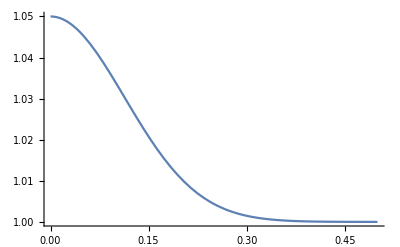

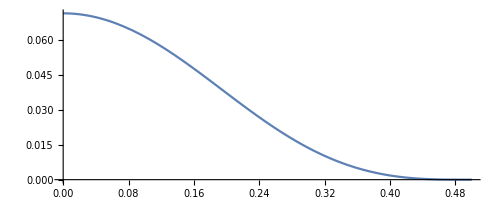

```mathematica
Clear[γ,R,SolLagrangian,solLagrangian,EB,px,py];

(* parameters *)
w = 0.010;
L0=0.125;
h = 0.015;
kf =0.01;
(*Q = 0.1;
n = 2;*)

k=(12*kf*L0^4)/(w*h^3);
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=10;
γ[S_]=1+dt*W[S];
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1;
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R0}];
Plot[γ[S],{S,0,1/2}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSolLagrangian[R/.SolLagrangian[[1]]]],{S,0,L/2}]
```

```mathematica
(* first step *)
grs={};
γ[S_]=1+dt*W[S];
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R/.SolLagrangian}];
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
rs=R/.SolLagrangian;
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
```

```mathematica
(* second step *)
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.solLagrangian,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R/.SolLagrangian}];
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
re=R/.SolLagrangian[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
```

```mathematica
(* Iterate the solution over time now *) 
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.45;
MaxFails=100;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.solLagrangian,{S,0,L/2}]];
P2=Plot[nx[S]/.solLagrangian,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
While[flag==0,
t = (re - rs);
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.solLagrangian,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
SolLagrangian=Quiet[Reap[FindRoot[RodOdeLagrangian[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeLagrangian[R/.SolLagrangian[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
Clear[γ];
γ = γOld;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
rs = re;
re = R/.SolLagrangian[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.solLagrangian,{S,0,L/2}]];
P2=Plot[nx[S]/.solLagrangian,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

Part::partd: Part specification Sol ⟦ 2 ⟧ is longer than depth of object.

0.0625

Part::partd: Part specification Sol ⟦ 2 ⟧ is longer than depth of object.

0.078125

Part::partd: Part specification Sol ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0.0976563

0.12207

0.152588

0.190735

0.238419

0.298023

0.149012

0.186265

0.0931323

0.116415

0.145519

0.0727596

0.0909495

0.0454747

0.0227374

0.0284217

0.0355271

0.0444089

0.0555112

0.0693889

0.0867362

0.10842

0.135525

0.169407

0.211758

0.105879

0.132349

0.165436

0.206795

0.258494

0.323117

0.403897

0.201948

0.100974

0.0504871

0.0252435

0.0126218

0.00631089

0.00315544

0.00157772

0.000788861

0.00039443

0.000197215

0.0000986076

0.0000493038

$Aborted

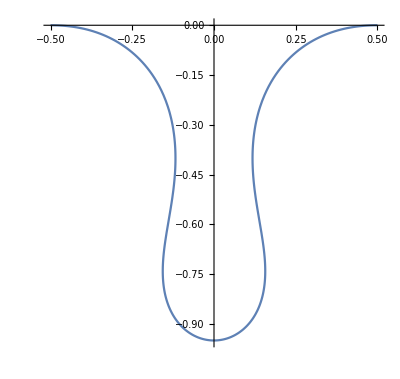

```mathematica
ParametricPlot[{{x[S],-y[S]},{-x[S], -y[S]}}/.solLagrangian,{S, 0, 1/2},PlotRange-> Full]
```

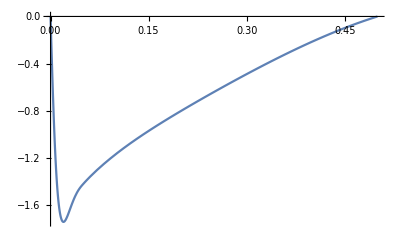

```mathematica
Plot[(θ[S])/.solLagrangian,{S, 0, 0.5},PlotRange-> Full]
```

```mathematica
WntScale=NIntegrate[W[S],{S, 0, 0.5}]
```

0.32716

```mathematica
WntScale=NIntegrate[W[s],{s, 0, l}]
```

Check the homogeneous stress

We need to define the homeostatic shape, (x[s], y[s]), which are defined by θ[s] and subsequently, m=θ’[s].

```mathematica
sValues=Range[0,1,.01];
```

```mathematica
l=s[0.5]/.solLagrangian
```

1.25927

```mathematica
S0Mesh = Range[0, 0.5, 0.005];
```

```mathematica
xHom=Interpolation[Table[{s[S0Mesh[[i]]],x[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
yHom=Interpolation[Table[{s[S0Mesh[[i]]],y[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
θHom=Interpolation[Table[{s[S0Mesh[[i]]],θ[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
mHom=Interpolation[Table[{s[S0Mesh[[i]]],m[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
```

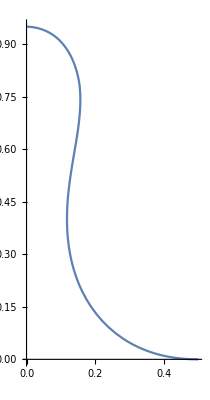

```mathematica
ParametricPlot[{xHom[s],yHom[s]},{s, 0, l}]
```

## Homeostasis ODEs

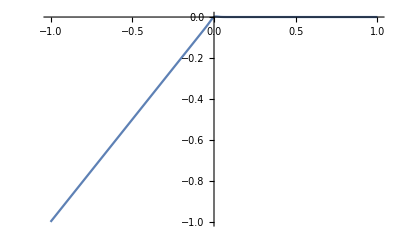

```mathematica
f=Function[m,m*1/2(1+Tanh[-50m])];
Plot[f[ns],{ns,-1,1}]
```

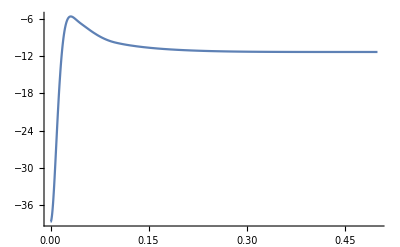

```mathematica
Plot[nx[S]/.solLagrangian,{S, 0, 1/2},PlotRange-> Full]
```

```mathematica
W[0]+(μ*(n0-ns)/.ParSubs)
```

0.5

```mathematica
k
```

868.056

```mathematica
ParSubs={k-> 1000,μ-> 0.25,ρ->10,ns->-20,n0->-22.5,β->.5};
eps=0.001;
HomeostasisSol=NDSolve[{v'[s]==((k (xHom[s]-px[s])*Cos[θHom[s]]+k (yHom[s]-py[s])*Sin[θHom[s]]+mHom[s]*(ny[s]*Cos[θHom[s]]-nx[s]*Sin[θHom[s]]))/(1+nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]))v[s]-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]),
nx'[s]==k (xHom[s]-px[s]),
ny'[s]==k*(yHom[s]-py[s]),
px'[s]==ρ (px[s]-xHom[s])/v[s],
py'[s]==ρ*(py[s]-yHom[s])/v[s],
nx[eps]==n0,
ny[eps]==0,
px[eps]==eps*ρ/(ρ+(W[0]+μ*f[n0-ns])),
py[eps]==0,
v[eps]==-eps*(W[0]+μ*f[n0-ns])}/.ParSubs,
{v,nx,ny,px,py},{s,eps,l},MaxStepSize-> 0.005][[1]];
```

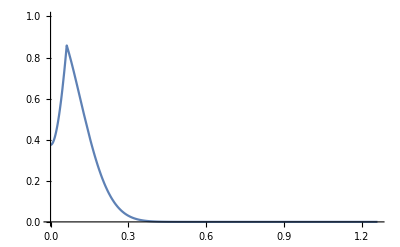

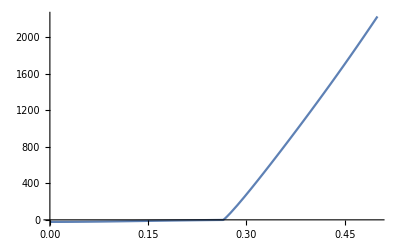

```mathematica
Plot[(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns])/.ParSubs/.HomeostasisSol,{s, eps, l},PlotRange-> {0, 1}]
Plot[(nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]])/.HomeostasisSol,{s, eps, 0.5},PlotRange-> Full]
```